```mathematica
import = Import["/Users/gpatenotte/Downloads/NaRb_PerturbTheory_J1M0.agr","CSV"];
```

```mathematica
dataStart=Position[import,{"@type xy"}][[All,1]]+1;
```

```mathematica
data1=import[[dataStart[[1]];;dataStart[[1]]+21000]];
data2=import[[dataStart[[2]];;dataStart[[2]]+21000]];
data3=import[[dataStart[[3]];;dataStart[[3]]+21000]];
```

```mathematica
makeX[data_]:=Table[StringTake[data[[n,1]],1;;StringPosition[data[[n,1]]," "][[1,1]]-1],{n,1,Length[data]}];
makeY[data_]:=Table[StringTake[data[[n,1]],StringPosition[data[[n,1]]," "][[1,1]];;-1],{n,1,Length[data]}];
makeXY[data_]:=Transpose@(ToExpression/@{makeX[data],makeY[data]});
```

```mathematica
par=makeXY[data3];
perp=makeXY[data2];
par[[All,1]]=10^7/par[[All,1]]-880.308;
perp[[All,1]]=10^7/perp[[All,1]]-880.308;
rat=Transpose@{par[[All,1]],-1+par[[All,2]]/perp[[All,2]]};
delta=Transpose@{par[[All,1]],par[[All,2]]-perp[[All,2]]};
```

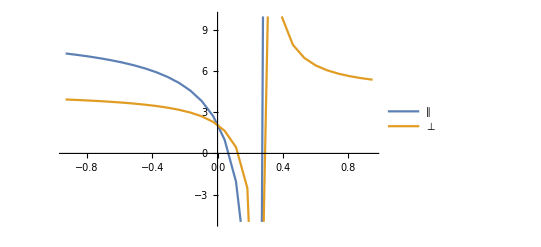

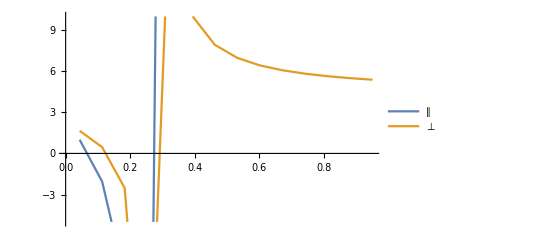

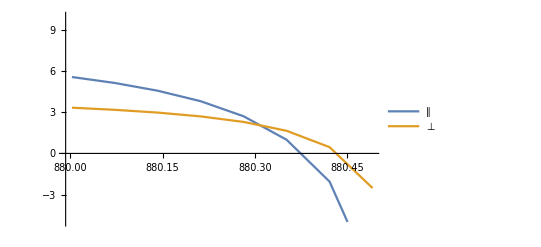

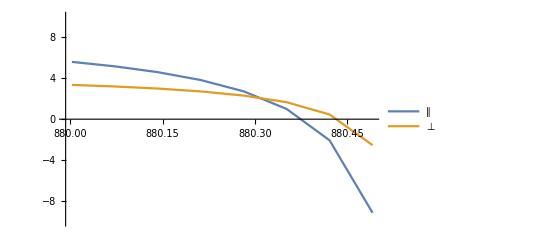

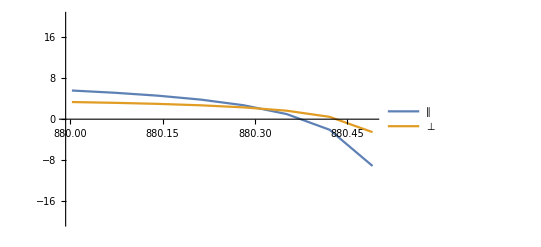

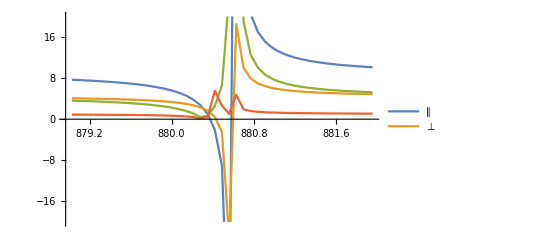

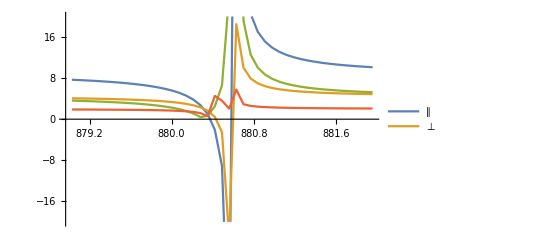

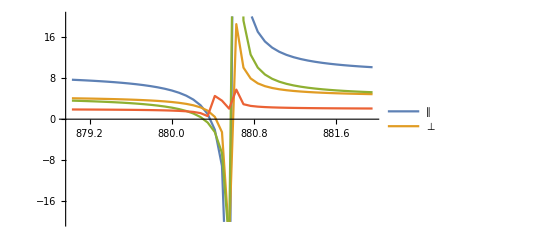

-Graphics-

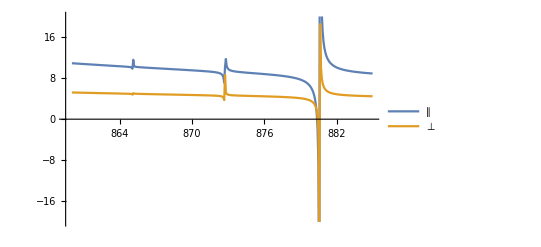

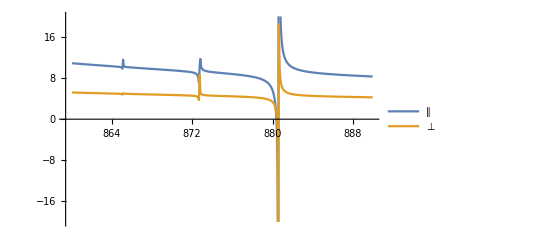

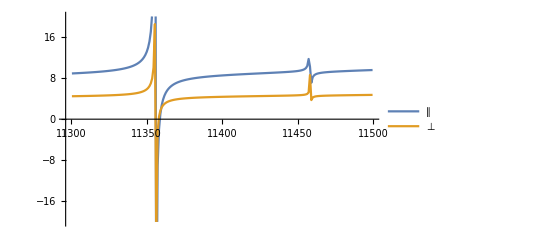

```mathematica
ListPlot[Select[#,-1<=#[[1]]<=1&]&/@{par,perp},PlotRange->{-5,10},Joined->True,PlotLegends->{"∥","⊥"},ImageSize->Full]
(*ListPlot[{par,perp},Joined->True]*)
(*ListPlot[{par,perp},PlotRange->{-20,20},Joined->False,PlotLegends->{"∥","⊥"},ImageSize->Full]*)
```

```mathematica
UnitConvert[Quantity["SpeedOfLight"]/Quantity[29.98 11360,"Gigahertz"],"Nanometers"]
```

880.26 nm

```mathematica
UnitConvert[Quantity["SpeedOfLight"]/Quantity[879.26,"Nanometers"],"Gigahertz"]/29.98
```

11372.9 GHz

```mathematica
SortBy[#,Abs[#[[1]]-11372.9]&][[1]]&/@{par,perp}
```

{{11372.6,7.38916},{11372.6,3.96898}}

```mathematica
par[[All,1]]=10^7/par[[All,1]]
```

299792458 m/s

$Aborted

{{11360,2.71068},{11360,2.29806}}

11360. GHz

$Failed

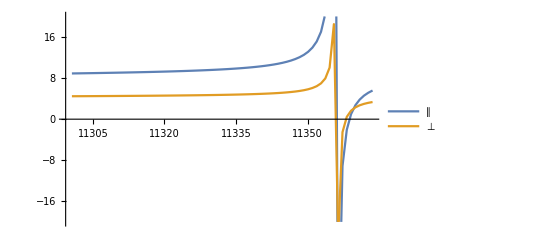

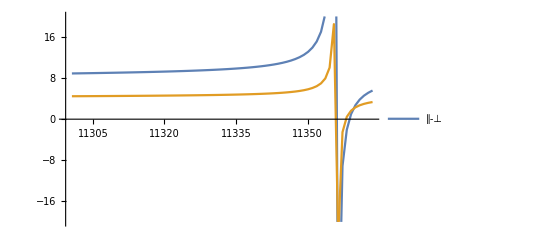

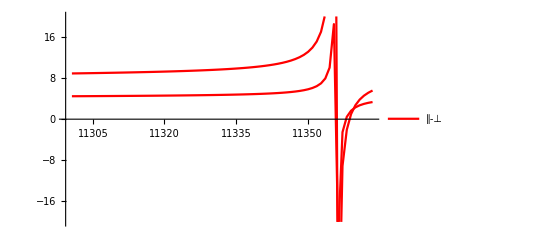

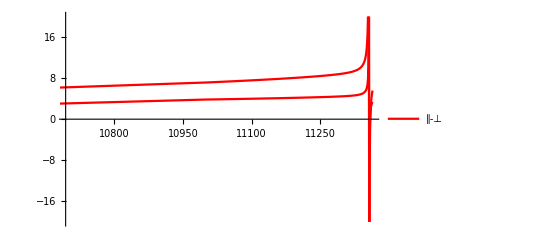

```mathematica
UnitConvert[Quantity["SpeedOfLight"]]
```

{{11450,9.38202},{11450,4.65359}}

{{11344.7,10.9679},{11344.7,5.14773}}

{{11299.7,8.89105},{11299.7,4.46147}}

{{10000,4.05045},{10000,1.35004}}

{{{10000,4.05045},{11000,7.14011},{11000.9,7.1436},{11001.8,7.14711},{11002.7,7.15061},{11003.6,7.15412},{11004.5,7.15764},{11005.4,7.16116},{11006.3,7.16469},{11007.2,7.16822},{11008.1,7.17175},{11009,7.17529},{11009.9,7.17884},{11010.8,7.18239},{11011.7,7.18594},{11012.6,7.1895},{11013.5,7.19306},{11014.4,7.19663},{11015.3,7.20021},{11016.2,7.20379},{11017.1,7.20737},{11018,7.21096},{11018.9,7.21456},{11019.8,7.21815},{11020.7,7.22176},{11021.6,7.22537},{11022.5,7.22898},{11023.4,7.2326},{11024.3,7.23623},{11025.2,7.23986},{11026.1,7.24349},{11027,7.24714},{11027.9,7.25078},{11028.8,7.25443},{11029.7,7.25809},{11030.6,7.26175},{11031.5,7.26542},{11032.4,7.26909},{11033.3,7.27276},{11034.2,7.27645},{11035.1,7.28014},{11036,7.28383},{11036.9,7.28753},{11037.8,7.29123},{11038.7,7.29494},{11039.6,7.29866},{11040.5,7.30238},{11041.4,7.3061},{11042.3,7.30983},{11043.2,7.31357},{11044.1,7.31731},{11045,7.32106},{11045.9,7.32481},{11046.8,7.32857},{11047.7,7.33234},{11048.6,7.33611},{11049.5,7.33988},{11050.4,7.34367},{11051.3,7.34745},{11052.2,7.35125},{11053.1,7.35504},{11054,7.35885},{11054.9,7.36266},{11055.8,7.36648},{11056.7,7.3703},{11057.6,7.37412},{11058.5,7.37796},{11059.4,7.3818},{11060.3,7.38564},{11061.2,7.38949},{11062.1,7.39335},{11063,7.39721},{11063.9,7.40108},{11064.8,7.40496},{11065.7,7.40884},{11066.6,7.41273},{11067.5,7.41662},{11068.4,7.42052},{11069.3,7.42443},{11070.2,7.42834},{11071.1,7.43226},{11072,7.43618},{11072.9,7.44011},{11073.8,7.44405},{11074.7,7.44799},{11075.6,7.45194},{11076.5,7.4559},{11077.4,7.45986},{11078.3,7.46383},{11079.2,7.4678},{11080.1,7.47178},{11081,7.47577},{11081.9,7.47977},{11082.8,7.48377},{11083.7,7.48777},{11084.6,7.49179},{11085.5,7.49581},{11086.4,7.49984},{11087.3,7.50387},{11088.2,7.50791},{11089.1,7.51196},{11090,7.51601},{11090.9,7.52008},{11091.8,7.52414},{11092.7,7.52822},{11093.6,7.5323},{11094.5,7.53639},{11095.4,7.54048},{11096.3,7.54459},{11097.2,7.5487},{11098.1,7.55281},{11099,7.55694},{11099.9,7.56107},{11100.8,7.56521},{11101.7,7.56935},{11102.6,7.57351},{11103.5,7.57767},{11104.4,7.58183},{11105.3,7.58601},{11106.2,7.59019},{11107.1,7.59438},{11108,7.59858},{11108.9,7.60278},{11109.8,7.60699},{11110.7,7.61121},{11111.6,7.61544},{11112.5,7.61968},{11113.4,7.62392},{11114.3,7.62817},{11115.2,7.63243},{11116.1,7.63669},{11117,7.64097},{11117.9,7.64525},{11118.8,7.64954},{11119.7,7.65384},{11120.6,7.65815},{11121.5,7.66246},{11122.4,7.66678},{11123.3,7.67111},{11124.2,7.67545},{11125.1,7.6798},{11126,7.68415},{11126.9,7.68852},{11127.8,7.69289},{11128.7,7.69727},{11129.6,7.70166},{11130.5,7.70606},{11131.4,7.71046},{11132.3,7.71488},{11133.2,7.7193},{11134.1,7.72374},{11135,7.72818},{11135.9,7.73263},{11136.8,7.73709},{11137.7,7.74156},{11138.6,7.74604},{11139.5,7.75052},{11140.4,7.75502},{11141.3,7.75953},{11142.2,7.76404},{11143.1,7.76857},{11144,7.7731},{11144.9,7.77764},{11145.8,7.7822},{11146.7,7.78676},{11147.6,7.79133},{11148.5,7.79591},{11149.4,7.80051},{11150.3,7.80511},{11151.2,7.80972},{11152.1,7.81434},{11153,7.81898},{11153.9,7.82362},{11154.8,7.82827},{11155.7,7.83293},{11156.6,7.83761},{11157.5,7.84229},{11158.4,7.84699},{11159.3,7.8517},{11160.2,7.85641},{11161.1,7.86114},{11162,7.86588},{11162.9,7.87063},{11163.8,7.87539},{11164.7,7.88016},{11165.6,7.88495},{11166.5,7.88974},{11167.4,7.89455},{11168.3,7.89937},{11169.2,7.9042},{11170.1,7.90904},{11171,7.91389},{11171.9,7.91876},{11172.8,7.92364},{11173.7,7.92853},{11174.6,7.93343},{11175.5,7.93835},{11176.4,7.94328},{11177.3,7.94822},{11178.2,7.95317},{11179.1,7.95814},{11180,7.96312},{11180.9,7.96811},{11181.8,7.97312},{11182.7,7.97814},{11183.6,7.98317},{11184.5,7.98822},{11185.4,7.99328},{11186.3,7.99836},{11187.2,8.00345},{11188.1,8.00855},{11189,8.01367},{11189.9,8.0188},{11190.8,8.02395},{11191.7,8.02912},{11192.6,8.03429},{11193.5,8.03949},{11194.4,8.0447},{11195.3,8.04992},{11196.2,8.05516},{11197.1,8.06042},{11198,8.06569},{11198.9,8.07098},{11199.8,8.07629},{11200.7,8.08161},{11201.6,8.08695},{11202.5,8.09231},{11203.4,8.09768},{11204.3,8.10308},{11205.2,8.10849},{11206.1,8.11391},{11207,8.11936},{11207.9,8.12482},{11208.8,8.13031},{11209.7,8.13581},{11210.6,8.14133},{11211.5,8.14687},{11212.4,8.15244},{11213.3,8.15802},{11214.2,8.16362},{11215.1,8.16924},{11216,8.17488},{11216.9,8.18055},{11217.8,8.18623},{11218.7,8.19194},{11219.6,8.19767},{11220.5,8.20343},{11221.4,8.2092},{11222.3,8.215},{11223.2,8.22082},{11224.1,8.22667},{11225,8.23254},{11225.9,8.23843},{11226.8,8.24435},{11227.7,8.2503},{11228.6,8.25627},{11229.5,8.26227},{11230.4,8.26829},{11231.3,8.27435},{11232.2,8.28043},{11233.1,8.28653},{11234,8.29267},{11234.9,8.29884},{11235.8,8.30503},{11236.7,8.31126},{11237.6,8.31752},{11238.5,8.3238},{11239.4,8.33012},{11240.3,8.33648},{11241.2,8.34286},{11242.1,8.34928},{11243,8.35574},{11243.9,8.36223},{11244.8,8.36875},{11245.7,8.37532},{11246.6,8.38191},{11247.5,8.38855},{11248.4,8.39523},{11249.3,8.40195},{11250.2,8.4087},{11251.1,8.4155},{11252,8.42234},{11252.9,8.42923},{11253.8,8.43616},{11254.7,8.44313},{11255.6,8.45015},{11256.5,8.45722},{11257.4,8.46434},{11258.3,8.47151},{11259.2,8.47873},{11260.1,8.486},{11261,8.49332},{11261.9,8.5007},{11262.8,8.50814},{11263.7,8.51563},{11264.6,8.52318},{11265.5,8.5308},{11266.4,8.53847},{11267.3,8.54622},{11268.2,8.55402},{11269.1,8.5619},{11270,8.56984},{11270.9,8.57786},{11271.8,8.58595},{11272.7,8.59412},{11273.6,8.60237},{11274.5,8.61069},{11275.4,8.6191},{11276.3,8.6276},{11277.2,8.63618},{11278.1,8.64486},{11279,8.65363},{11279.9,8.66249},{11280.8,8.67146},{11281.7,8.68054},{11282.6,8.68972},{11283.5,8.69901},{11284.4,8.70842},{11285.3,8.71794},{11286.2,8.72759},{11287.1,8.73737},{11288,8.74729},{11288.9,8.75734},{11289.8,8.76753},{11290.7,8.77788},{11291.6,8.78838},{11292.5,8.79904},{11293.4,8.80987},{11294.3,8.82087},{11295.2,8.83206},{11296.1,8.84344},{11297,8.85502},{11297.9,8.86681},{11298.8,8.87882},{11299.7,8.89105},{11300.6,8.90352},{11301.5,8.91624},{11302.4,8.92922},{11303.3,8.94248},{11304.2,8.95603},{11305.1,8.96988},{11306,8.98406},{11306.9,8.99857},{11307.8,9.01343},{11308.7,9.02868},{11309.6,9.04432},{11310.5,9.06038},{11311.4,9.07689},{11312.3,9.09387},{11313.2,9.11135},{11314.1,9.12936},{11315,9.14795},{11315.9,9.16714},{11316.8,9.18698},{11317.7,9.20752},{11318.6,9.22879},{11319.5,9.25087},{11320.4,9.2738},{11321.3,9.29766},{11322.2,9.32251},{11323.1,9.34844},{11324,9.37555},{11324.9,9.40392},{11325.8,9.43368},{11326.7,9.46495},{11327.6,9.49788},{11328.5,9.53262},{11329.4,9.56937},{11330.3,9.60832},{11331.2,9.64974},{11332.1,9.69388},{11333,9.74108},{11333.9,9.79171},{11334.8,9.84621},{11335.7,9.90508},{11336.6,9.96896},{11337.5,10.0386},{11338.4,10.1148},{11339.3,10.1987},{11340.2,10.2916},{11341.1,10.3952},{11342,10.5116},{11342.9,10.6433},{11343.8,10.7939},{11344.7,10.9679},{11345.6,11.1714},{11346.5,11.4131},{11347.4,11.7051},{11348.3,12.0653},{11349.2,12.5216},{11350.1,13.1191},{11351,13.9367},{11351.9,15.1255},{11352.8,17.0171},{11353.7,20.5098},{11354.6,29.2336},{11355.5,106.553},{11356.4,-47.3704},{11357.3,-9.11361},{11358.2,-2.05986},{11359.1,0.995999},{11360,2.71068},{11360.9,3.81063},{11361.8,4.57735},{11362.7,5.1431},{11363.6,5.57827}},{{10000,1.35004},{11000,3.82226},{11000.9,3.82359},{11001.8,3.82491},{11002.7,3.82624},{11003.6,3.82757},{11004.5,3.8289},{11005.4,3.83024},{11006.3,3.83157},{11007.2,3.83291},{11008.1,3.83425},{11009,3.83559},{11009.9,3.83693},{11010.8,3.83828},{11011.7,3.83962},{11012.6,3.84097},{11013.5,3.84232},{11014.4,3.84367},{11015.3,3.84502},{11016.2,3.84637},{11017.1,3.84773},{11018,3.84909},{11018.9,3.85045},{11019.8,3.85181},{11020.7,3.85317},{11021.6,3.85453},{11022.5,3.8559},{11023.4,3.85727},{11024.3,3.85864},{11025.2,3.86001},{11026.1,3.86138},{11027,3.86276},{11027.9,3.86413},{11028.8,3.86551},{11029.7,3.86689},{11030.6,3.86827},{11031.5,3.86966},{11032.4,3.87104},{11033.3,3.87243},{11034.2,3.87382},{11035.1,3.87521},{11036,3.8766},{11036.9,3.878},{11037.8,3.8794},{11038.7,3.88079},{11039.6,3.88219},{11040.5,3.8836},{11041.4,3.885},{11042.3,3.88641},{11043.2,3.88781},{11044.1,3.88923},{11045,3.89064},{11045.9,3.89205},{11046.8,3.89347},{11047.7,3.89488},{11048.6,3.8963},{11049.5,3.89772},{11050.4,3.89915},{11051.3,3.90057},{11052.2,3.902},{11053.1,3.90343},{11054,3.90486},{11054.9,3.90629},{11055.8,3.90773},{11056.7,3.90916},{11057.6,3.9106},{11058.5,3.91204},{11059.4,3.91349},{11060.3,3.91493},{11061.2,3.91638},{11062.1,3.91783},{11063,3.91928},{11063.9,3.92073},{11064.8,3.92219},{11065.7,3.92365},{11066.6,3.9251},{11067.5,3.92657},{11068.4,3.92803},{11069.3,3.92949},{11070.2,3.93096},{11071.1,3.93243},{11072,3.9339},{11072.9,3.93538},{11073.8,3.93685},{11074.7,3.93833},{11075.6,3.93981},{11076.5,3.9413},{11077.4,3.94278},{11078.3,3.94427},{11079.2,3.94576},{11080.1,3.94725},{11081,3.94874},{11081.9,3.95024},{11082.8,3.95174},{11083.7,3.95324},{11084.6,3.95474},{11085.5,3.95625},{11086.4,3.95775},{11087.3,3.95926},{11088.2,3.96077},{11089.1,3.96229},{11090,3.9638},{11090.9,3.96532},{11091.8,3.96684},{11092.7,3.96837},{11093.6,3.96989},{11094.5,3.97142},{11095.4,3.97295},{11096.3,3.97448},{11097.2,3.97602},{11098.1,3.97756},{11099,3.9791},{11099.9,3.98064},{11100.8,3.98218},{11101.7,3.98373},{11102.6,3.98528},{11103.5,3.98683},{11104.4,3.98839},{11105.3,3.98995},{11106.2,3.99151},{11107.1,3.99307},{11108,3.99463},{11108.9,3.9962},{11109.8,3.99777},{11110.7,3.99934},{11111.6,4.00092},{11112.5,4.0025},{11113.4,4.00408},{11114.3,4.00566},{11115.2,4.00725},{11116.1,4.00883},{11117,4.01042},{11117.9,4.01202},{11118.8,4.01361},{11119.7,4.01521},{11120.6,4.01682},{11121.5,4.01842},{11122.4,4.02003},{11123.3,4.02164},{11124.2,4.02325},{11125.1,4.02487},{11126,4.02649},{11126.9,4.02811},{11127.8,4.02973},{11128.7,4.03136},{11129.6,4.03299},{11130.5,4.03462},{11131.4,4.03626},{11132.3,4.0379},{11133.2,4.03954},{11134.1,4.04118},{11135,4.04283},{11135.9,4.04448},{11136.8,4.04614},{11137.7,4.04779},{11138.6,4.04945},{11139.5,4.05112},{11140.4,4.05278},{11141.3,4.05445},{11142.2,4.05613},{11143.1,4.0578},{11144,4.05948},{11144.9,4.06116},{11145.8,4.06285},{11146.7,4.06454},{11147.6,4.06623},{11148.5,4.06793},{11149.4,4.06963},{11150.3,4.07133},{11151.2,4.07303},{11152.1,4.07474},{11153,4.07645},{11153.9,4.07817},{11154.8,4.07989},{11155.7,4.08161},{11156.6,4.08334},{11157.5,4.08507},{11158.4,4.0868},{11159.3,4.08854},{11160.2,4.09028},{11161.1,4.09203},{11162,4.09377},{11162.9,4.09553},{11163.8,4.09728},{11164.7,4.09904},{11165.6,4.10081},{11166.5,4.10257},{11167.4,4.10434},{11168.3,4.10612},{11169.2,4.1079},{11170.1,4.10968},{11171,4.11147},{11171.9,4.11326},{11172.8,4.11506},{11173.7,4.11686},{11174.6,4.11866},{11175.5,4.12047},{11176.4,4.12228},{11177.3,4.1241},{11178.2,4.12592},{11179.1,4.12774},{11180,4.12957},{11180.9,4.13141},{11181.8,4.13325},{11182.7,4.13509},{11183.6,4.13694},{11184.5,4.13879},{11185.4,4.14065},{11186.3,4.14251},{11187.2,4.14437},{11188.1,4.14625},{11189,4.14812},{11189.9,4.15},{11190.8,4.15189},{11191.7,4.15378},{11192.6,4.15568},{11193.5,4.15758},{11194.4,4.15949},{11195.3,4.1614},{11196.2,4.16332},{11197.1,4.16524},{11198,4.16717},{11198.9,4.1691},{11199.8,4.17104},{11200.7,4.17299},{11201.6,4.17494},{11202.5,4.17689},{11203.4,4.17885},{11204.3,4.18082},{11205.2,4.1828},{11206.1,4.18478},{11207,4.18676},{11207.9,4.18876},{11208.8,4.19075},{11209.7,4.19276},{11210.6,4.19477},{11211.5,4.19679},{11212.4,4.19881},{11213.3,4.20085},{11214.2,4.20288},{11215.1,4.20493},{11216,4.20698},{11216.9,4.20904},{11217.8,4.21111},{11218.7,4.21318},{11219.6,4.21526},{11220.5,4.21735},{11221.4,4.21945},{11222.3,4.22155},{11223.2,4.22366},{11224.1,4.22579},{11225,4.22791},{11225.9,4.23005},{11226.8,4.23219},{11227.7,4.23435},{11228.6,4.23651},{11229.5,4.23868},{11230.4,4.24086},{11231.3,4.24305},{11232.2,4.24525},{11233.1,4.24746},{11234,4.24967},{11234.9,4.2519},{11235.8,4.25414},{11236.7,4.25638},{11237.6,4.25864},{11238.5,4.26091},{11239.4,4.26319},{11240.3,4.26548},{11241.2,4.26778},{11242.1,4.27009},{11243,4.27241},{11243.9,4.27475},{11244.8,4.27709},{11245.7,4.27945},{11246.6,4.28183},{11247.5,4.28421},{11248.4,4.28661},{11249.3,4.28902},{11250.2,4.29144},{11251.1,4.29388},{11252,4.29633},{11252.9,4.2988},{11253.8,4.30128},{11254.7,4.30377},{11255.6,4.30629},{11256.5,4.30881},{11257.4,4.31136},{11258.3,4.31392},{11259.2,4.3165},{11260.1,4.31909},{11261,4.3217},{11261.9,4.32434},{11262.8,4.32699},{11263.7,4.32965},{11264.6,4.33234},{11265.5,4.33505},{11266.4,4.33778},{11267.3,4.34053},{11268.2,4.34331},{11269.1,4.3461},{11270,4.34892},{11270.9,4.35176},{11271.8,4.35463},{11272.7,4.35752},{11273.6,4.36044},{11274.5,4.36338},{11275.4,4.36636},{11276.3,4.36936},{11277.2,4.37239},{11278.1,4.37545},{11279,4.37854},{11279.9,4.38167},{11280.8,4.38482},{11281.7,4.38802},{11282.6,4.39124},{11283.5,4.39451},{11284.4,4.39781},{11285.3,4.40116},{11286.2,4.40454},{11287.1,4.40797},{11288,4.41144},{11288.9,4.41495},{11289.8,4.41852},{11290.7,4.42213},{11291.6,4.42579},{11292.5,4.42951},{11293.4,4.43328},{11294.3,4.43711},{11295.2,4.44101},{11296.1,4.44496},{11297,4.44898},{11297.9,4.45307},{11298.8,4.45723},{11299.7,4.46147},{11300.6,4.46578},{11301.5,4.47018},{11302.4,4.47466},{11303.3,4.47924},{11304.2,4.48391},{11305.1,4.48868},{11306,4.49355},{11306.9,4.49854},{11307.8,4.50364},{11308.7,4.50887},{11309.6,4.51422},{11310.5,4.51972},{11311.4,4.52536},{11312.3,4.53116},{11313.2,4.53712},{11314.1,4.54326},{11315,4.54958},{11315.9,4.5561},{11316.8,4.56284},{11317.7,4.5698},{11318.6,4.57701},{11319.5,4.58448},{11320.4,4.59222},{11321.3,4.60027},{11322.2,4.60865},{11323.1,4.61738},{11324,4.62649},{11324.9,4.63601},{11325.8,4.64599},{11326.7,4.65645},{11327.6,4.66746},{11328.5,4.67906},{11329.4,4.69131},{11330.3,4.70428},{11331.2,4.71804},{11332.1,4.73269},{11333,4.74832},{11333.9,4.76507},{11334.8,4.78306},{11335.7,4.80247},{11336.6,4.82348},{11337.5,4.84634},{11338.4,4.87132},{11339.3,4.89876},{11340.2,4.92908},{11341.1,4.96279},{11342,5.00056},{11342.9,5.0432},{11343.8,5.09179},{11344.7,5.14773},{11345.6,5.21291},{11346.5,5.28994},{11347.4,5.38249},{11348.3,5.49594},{11349.2,5.63845},{11350.1,5.82313},{11351,6.0723},{11351.9,6.42747},{11352.8,6.97546},{11353.7,7.93352},{11354.6,10.0416},{11355.5,18.5081},{11356.4,-23.1773},{11357.3,-2.52848},{11358.2,0.455073},{11359.1,1.65203},{11360,2.29806},{11360.9,2.70282},{11361.8,2.98052},{11362.7,3.18311},{11363.6,3.33763}}}

-Graphics-

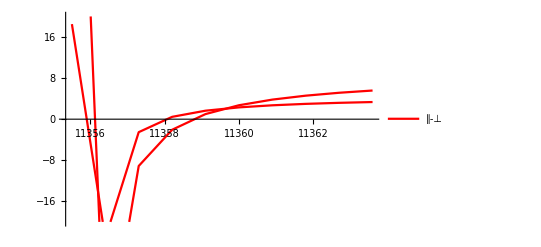

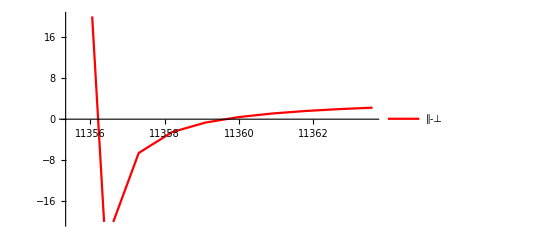

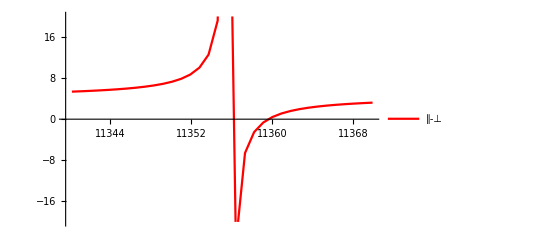

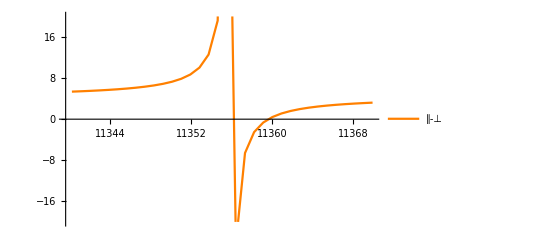

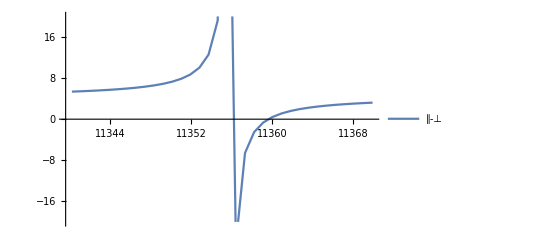

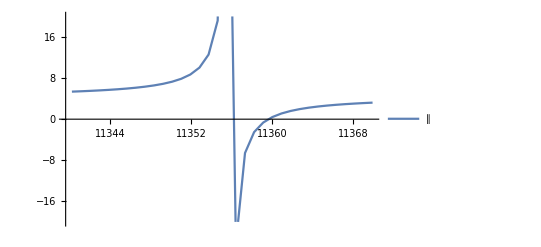

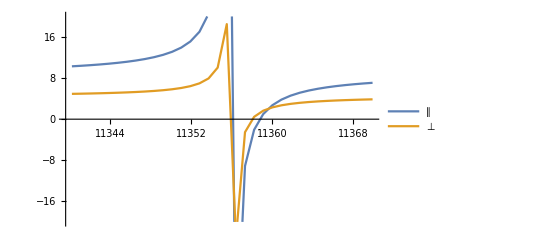

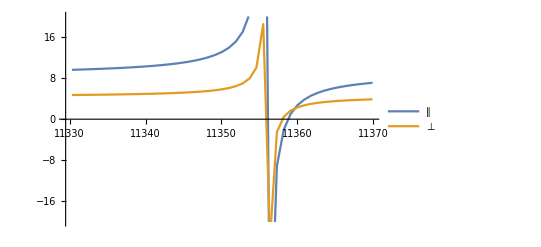

-Graphics-

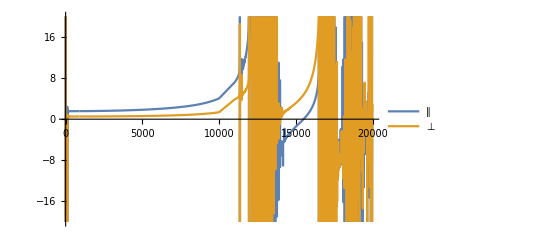

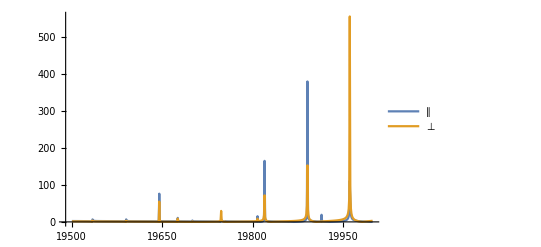

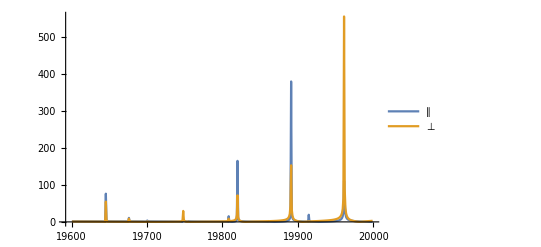

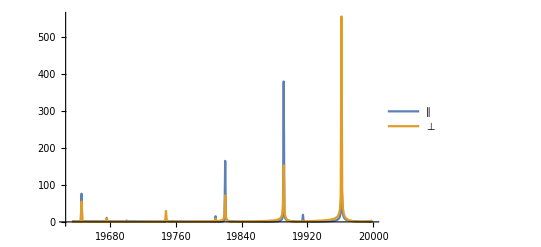

-Graphics-

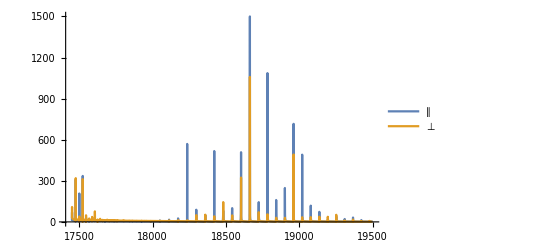

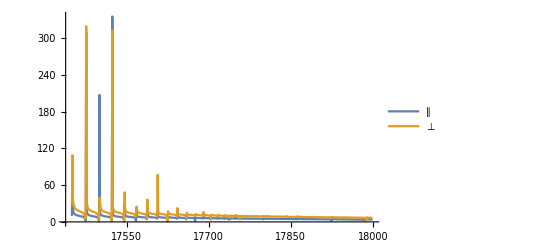

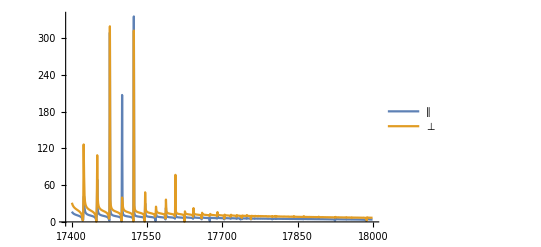

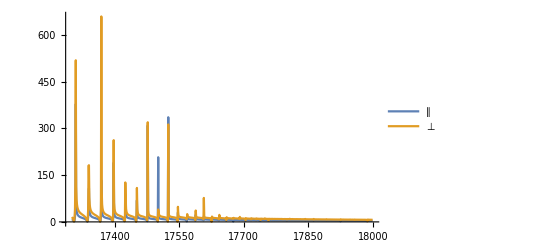

-Graphics-

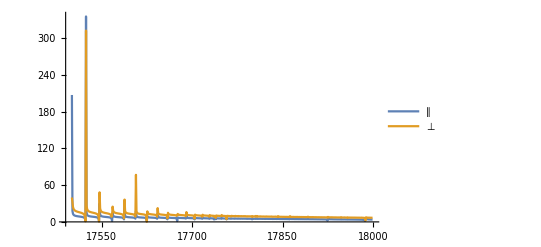

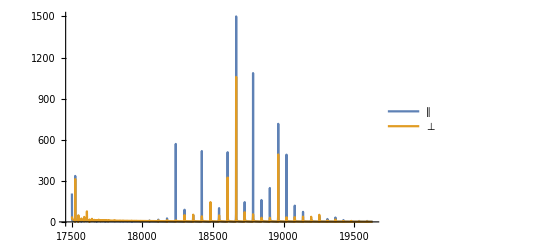

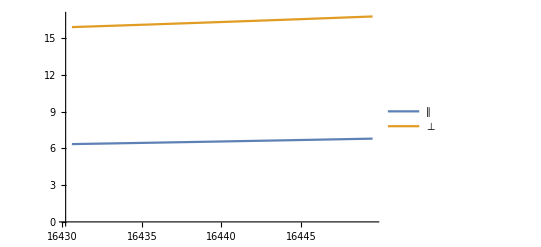

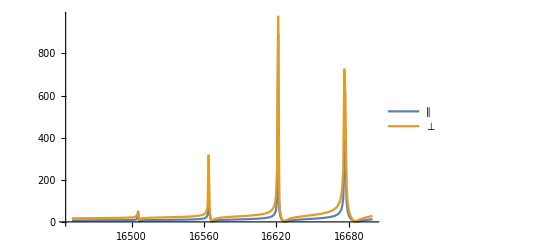

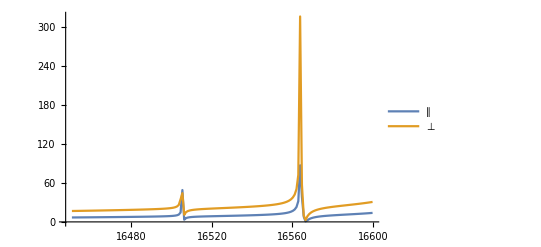

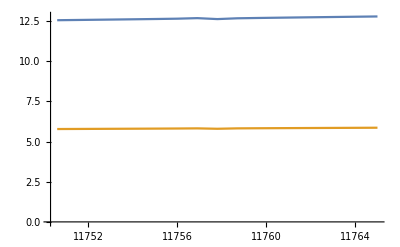

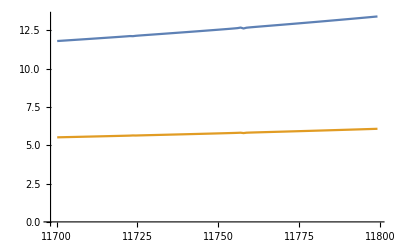

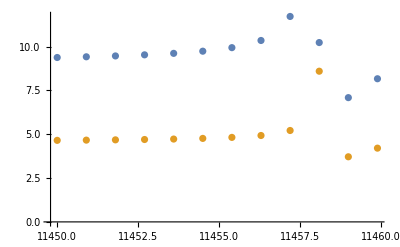

```mathematica
SortBy[#,Abs[#[[1]]-11450]&][[1]]&/@{par,perp}
```

```mathematica
Transpose@{par[[All,1]],par[[All,2]]-par[[All,1]]}
```